Define the polynomial

```mathematica
p[s_]=3 s^3+4 s-2;
```

Plot this

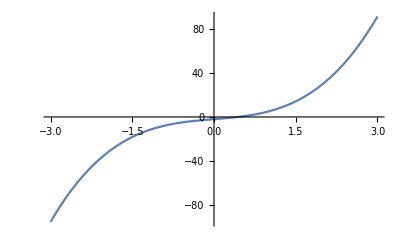

```mathematica
Plot[p[s],{s,-3,3}]
```

Use the Roots function to find the roots of the polynomial

```mathematica
roots1=Roots[p[s]==0,s]
```

s==1/3 (-4/(9+√145)^(1/3)+(9+√145)^(1/3))||s==(2 (1+ⅈ √3))/(3 (9+√145)^(1/3))-1/6 (1-ⅈ √3) (9+√145)^(1/3)||s==(2 (1-ⅈ √3))/(3 (9+√145)^(1/3))-1/6 (1+ⅈ √3) (9+√145)^(1/3)

```mathematica
roots1//N
```

s==0.437287||s==-0.218643+1.21522 ⅈ||s==-0.218643-1.21522 ⅈ

Use the ‘Solve’ function to find the roots of the polynomial

```mathematica
roots2=Solve[p[s]==0,s]
```

{{s→1/3 (-4/(9+√145)^(1/3)+(9+√145)^(1/3))},{s→(2 (1+ⅈ √3))/(3 (9+√145)^(1/3))-1/6 (1-ⅈ √3) (9+√145)^(1/3)},{s→(2 (1-ⅈ √3))/(3 (9+√145)^(1/3))-1/6 (1+ⅈ √3) (9+√145)^(1/3)}}

```mathematica
roots2//N
```

{{s→0.437287},{s→-0.218643+1.21522 ⅈ},{s→-0.218643-1.21522 ⅈ}}